```mathematica
ClearAll[p1,p2,p3];
(*Ищет параметры*)
FindParametres[a1_,a2_,a3_,T_]:=Module[{r=Sqrt[a1^2+a2^2], p1,p2,p3,e=10^-4,tz,t},
If[r==0&&a3≠0,
tz=2Pi;p1=-Sqrt[a3/Pi]; p2=0,
tz=t/.FindRoot[8 a3/r^2-(t-Sin[t])/Sin[t/2]^2,{t,6}];
p3=tz/T;
p1=0.5p3(-a1 +a2 Sin[tz]/(1-Cos[tz]));p2=-0.5p3(a1  Cot[tz/2]+a2 )
];
If[Abs[p1]<e,p1=0];
If[Abs[p2]<e,p2=0];
If[p3<e,p3=0];
{p1,p2,p3}];

(* Выводит функции x_i*)
FindXi[a1_,a2_,a3_,T_]:=Module[{p1,p2,p3,u1,u2,x1,x2,x3,x4,x5,x6,x7,x8},
{p1,p2,p3}=FindParametres[a1,a2,a3,T];
u1[t_]:= -(p2 Cos[p3 t]+p1 Sin[p3 t]);
u2[t_]:= p1 Cos[p3 t]-p2 Sin[p3 t];
x1[t_]:=-1/p3(p1-p1 Cos[p3 t]+p2 Sin[p3 t]);
x2[t_]:=1/p3(-p2+p2 Cos[p3 t]+ p1 Sin[p3 t]);
x3[t_]:=(p1^2+p2^2)/(2p3^2)(p3 t-Sin[p3 t]);
x4[t_]:=1/(4 p3^3)(-3 p1^2 p2-3 p2^3-2 p1^3 p3 t-2 p1 p2^2 p3 t+4 p1^2 p2 Cos[p3 t]+4 p2^3 Cos[p3 t]-p1^2 p2 Cos[2 p3 t]-p2^3 Cos[2 p3 t]+4 p1^3 Sin[p3 t]+4 p1 p2^2 Sin[p3 t]-p1^3 Sin[2 p3 t]-p1 p2^2 Sin[2 p3 t]);
x5[t_]:= 1/(4 p3^3)(3 p1^3+3 p1 p2^2-2 p1^2 p2 p3 t-2 p2^3 p3 t-4 p1^3 Cos[p3 t]-4 p1 p2^2 Cos[p3 t]+p1^3 Cos[2 p3 t]+p1 p2^2 Cos[2 p3 t]+4 p1^2 p2 Sin[p3 t]+4 p2^3 Sin[p3 t]-p1^2 p2 Sin[2 p3 t]-p2^3 Sin[2 p3 t]);
x6[t_]:= 1/(192 p3^4)(60 p1^3 p2+52 p1 p2^3+60 p1^4 p3 t+72 p1^2 p2^2 p3 t+12 p2^4 p3 t-104 p1^3 p2 Cos[p3 t]-72 p1 p2^3 Cos[p3 t]+64 p1^3 p2 Cos[2 p3 t]+16 p1 p2^3 Cos[2 p3 t]-24 p1^3 p2 Cos[3 p3 t]+8 p1 p2^3 Cos[3 p3 t]+4 p1^3 p2 Cos[4 p3 t]-4 p1 p2^3 Cos[4 p3 t]-104 p1^4 Sin[p3 t]-72 p1^2 p2^2 Sin[p3 t]+32 p1^4 Sin[2 p3 t]-24 p1^2 p2^2 Sin[2 p3 t]-8 p2^4 Sin[2 p3 t]-8 p1^4 Sin[3 p3 t]+24 p1^2 p2^2 Sin[3 p3 t]+p1^4 Sin[4 p3 t]-6 p1^2 p2^2 Sin[4 p3 t]+p2^4 Sin[4 p3 t]);
x7[t_]:= 1/(48 p3^4)(-10 p1^4+10 p2^4+24 p1^3 p2 p3 t+24 p1 p2^3 p3 t+15 p1^4 Cos[p3 t]-15 p2^4 Cos[p3 t]-6 p1^4 Cos[2 p3 t]+6 p2^4 Cos[2 p3 t]+p1^4 Cos[3 p3 t]-p2^4 Cos[3 p3 t]-42 p1^3 p2 Sin[p3 t]-42 p1 p2^3 Sin[p3 t]+12 p1^3 p2 Sin[2 p3 t]+12 p1 p2^3 Sin[2 p3 t]-2 p1^3 p2 Sin[3 p3 t]-2 p1 p2^3 Sin[3 p3 t]);
x8[t_]:=1/(192 p3^4)(-52 p1^3 p2-60 p1 p2^3+12 p1^4 p3 t+72 p1^2 p2^2 p3 t+60 p2^4 p3 t+72 p1^3 p2 Cos[p3 t]+104 p1 p2^3 Cos[p3 t]-16 p1^3 p2 Cos[2 p3 t]-64 p1 p2^3 Cos[2 p3 t]-8 p1^3 p2 Cos[3 p3 t]+24 p1 p2^3 Cos[3 p3 t]+4 p1^3 p2 Cos[4 p3 t]-4 p1 p2^3 Cos[4 p3 t]-72 p1^2 p2^2 Sin[p3 t]-104 p2^4 Sin[p3 t]-8 p1^4 Sin[2 p3 t]-24 p1^2 p2^2 Sin[2 p3 t]+32 p2^4 Sin[2 p3 t]+24 p1^2 p2^2 Sin[3 p3 t]-8 p2^4 Sin[3 p3 t]+p1^4 Sin[4 p3 t]-6 p1^2 p2^2 Sin[4 p3 t]+p2^4 Sin[4 p3 t]);

{x1[t],x2[t],x3[t],x4[t],x5[t],x6[t],x7[t],x8[t]}];


(* Выводит функции x_1 x_2*)
FindX12[a1_,a2_,a3_,T_]:=Module[{p1,p2,p3,x1,x2},
{p1,p2,p3}=FindParametres[a1,a2,a3,T];
x1[t_]=-1/p3(p1-p1 Cos[p3 t]+p2 Sin[p3 t]);
x2[t_]=1/p3(-p2+p2 Cos[p3 t]+ p1 Sin[p3 t]);
{x1[t],x2[t]}];

(*Выводит центр тяжести и моменты инерции, Xc,Yc,J1,K12,J2*)
FindMoments[a1_,a2_,a3_,T_] := Module[{Xc,Yc,r, x1,x2,x3,x4,x5,x6,x7,x8},
{x1,x2,x3,x4,x5,x6,x7,x8}=FindXi[a1,a2,a3,T];
r = a1^2+a2^2;
Xc=(x4/.t->T)/a3-a2 r/6/a3;
Yc=(x5/.t->T)/a3+a1 r/6/a3;
{Xc, Yc, 2(x8/.t->T)+a1 a2^3/12 -a3 Yc^2,(x7/.t->T)-a3 Yc Xc, 2(x6/.t->T)-a1^3 a2/12-a3 Xc^2}];

(*Рисует элипс инерции*)
ShowEllipse[a1_,a2_,a3_,T_]:=Module[{Xc,Yc,J1,J2,K12, p1,p2,p3,x1,x2},
{Xc,Yc,J1,K12,J2}=FindMoments[a1,a2,a3,T];
{p1,p2,p3}=FindParametres[a1,a2,a3,T];
x1[t_]=-1/p3(p1-p1 Cos[p3 t]+p2 Sin[p3 t]);
x2[t_]=1/p3(-p2+p2 Cos[p3 t]+ p1 Sin[p3 t]);
Show[If [T==2Pi/p3,ParametricPlot[{x1[t],x2[t]},{t,0,T}, PlotRange->All], {ParametricPlot[{x1[t],x2[t]},{t,0,T}, PlotRange->All],Plot[x2[T]/x1[T]s, {s,0, x1[T]}]} ],
ContourPlot[J1 (w1-Xc)^2-2K12 (w1-Xc) (w2-Yc)+J2 (w2-Yc)^2==1, {w1,-10,10},{w2,-10,10}]]
];
```

```mathematica
FindJ1[teta_, r_] := Module[{a3=Pi/2,T=Pi, Yc, a1 = r Cos[teta], a2 = r Sin[teta], b, S, J},
{x1,x2,x3,x4,x5,x6,x7,x8}=FindXi[a1,a2,a3,T];
Yc=(x5/.t->T)/a3+a1(a1^2+a2^2)/6/a3;
J = 2(x8/.t->T)+a1 a2^3/12 -a3 Yc^2;
S = (x5/.t->T)+a1(a1^2+a2^2)/6;
min = FindMinimum[FindX12[a1,a2,a3,T][[1]], {t, 2}][[1]];
max = FindMaximum[FindX12[a1,a2,a3,T][[1]], {t, 2}][[1]];
b = max - min;
S/(b*J)];

FindT[a1_,a2_,a3_,T_]:= Module[{x2,Yc},
x2 = FindXi[a1,a2,a3,T][[2]];
Yc = FindMoments[a1,a2,a3,T][[2]];
FindRoot[x2==Yc, {t, 1}][[1]][[2]]]
```

```mathematica
{Xc,Yc,J1,K12,J2}=FindMoments[1,2,1,T]
```

```mathematica
{0.7316121211570403,0.8841939394214807,0.6477970205690238,-0.6468870035343491+0.22616082294956802 (2.9599887704528465+0.14436467060459438 u2$12630),0.07593804706788243}
```

{0.731612,0.884194,0.647797,-0.646887+0.226161 (2.95999+0.144365 u2$12630),0.075938}

```mathematica
(*Для построения графика. my*)
ShowEllipse2[a1_,a2_,a3_,T_]:=Module[{Xc,Yc,J1,J2,K12, p1,p2,p3,x1,x2},
{Xc,Yc,J1,K12,J2}=FindMoments[a1,a2,a3,T];
ContourPlot[J1 (w1-Xc)^2-2K12 (w1-Xc) (w2-Yc)+J2 (w2-Yc)^2==1, {w1,-6,6},{w2,-6,6}, PlotRange->All]
];
T = Pi;
a3 = Pi/2;
Manipulate[Show[ParametricPlot[{FindX12[a1,a2,a3,T][[1]],FindX12[a1,a2,a3,T][[2]]},{t,0,T},PlotRange->{-5,5}, AxesLabel->{x1,x2},AxesStyle->Directive[FontSize->12, Arrowheads[{0.0, 0.05}]]],ShowEllipse2[a1,a2,a3,T],Graphics[Line[{{0,0},{a1,a2}}]]],
{{a1,1,"a1"},-3,3},{{a2,0,"a2"},-3,3}]
(*table,flat*)
```

```mathematica
{}
```

```mathematica
With[{p={x,5}},Table[x^2,p]]
```

{1,4,9,16,25}

```mathematica
Anim=With[{p = {a1,-3,3},b = {a2,-3,3}},Table[Show[ParametricPlot[{FindX12[a1,a2,a3,T][[1]],FindX12[a1,a2,a3,T][[2]]},{t,0,T},PlotRange->{-5,5}, AxesLabel->{x1,x2},AxesStyle->Directive[FontSize->12, Arrowheads[{0.0, 0.05}]]],ShowEllipse2[a1,a2,a3,T],Graphics[Line[{{0,0},{a1,a2}}]]],p,b]];
```

```mathematica
(*Для выгрузки анимации:Animat = Flatten[Anim];
```

```mathematica
Export["/home/irina/Downloads/Name/Animat.gif",Animat];*)
```

```mathematica
a3 = Pi/2;
Manipulate[Show[ShowEllipse2[a1,a2,a3,T],ParametricPlot[{FindX12[a1,a2,a3,T][[1]],FindX12[a1,a2,a3,T][[2]]},{t,0,T},PlotRange->{{-4,4},{0-4,4}}],Graphics[Line[{{0,0},{a1,a2}}]]
],
{{a1,1,"a1"},-4,4},{{a2,0,"a2"},-4,4}]
```

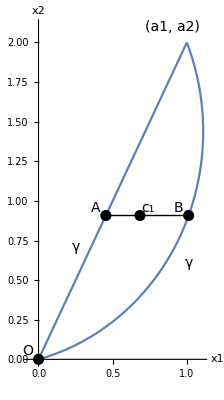

```mathematica
(*Пример расчета*)
a1 = 1;
a2 = 2;
T=1/2Pi;
a3 = 1/4Pi;
XC = FindMoments[a1,a2,a3,T][[1]];
YC = FindMoments[a1,a2,a3,T][[2]];
A = a1/a2*YC;
T2=FindT[a1,a2,a3,T];
x11 = FindX12[a1,a2,a3,T][[1]];
B = x11/.t->T2;
Show[ParametricPlot[{FindX12[a1,a2,a3,T][[1]],FindX12[a1,a2,a3,T][[2]]},{t,0,T}, AxesStyle->Arrowheads[{0.0, 0.05}], AxesLabel->{"x1","x2"}, LabelStyle->FontSize->14], Plot[a2/a1 s, {s,0, a1}],
Graphics[{PointSize[0.02],Point[{{XC,YC}},VertexColors->{Black}]}],
Graphics[Text[Style["(a1, a2)",FontSize->14],{a1-0.1,a2+0.1}]],
Graphics[Text[Style[Subscript[c,1], FontSize->14],{XC+0.05,YC+0.05}]],
Graphics[{PointSize[0.02],Point[{{A,YC}},VertexColors->{Black}]}],
Graphics[Text[Style["A",FontSize->14],{A-0.07,YC+0.05}]],
Graphics[{PointSize[0.02],Point[{B,YC},VertexColors->{Black}]}],
Graphics[Text[Style["B",FontSize->14],{B-0.07,YC+0.05}]],
Graphics[{PointSize[0.02],Point[{0,0},VertexColors->{Black}]}],
Graphics[Text[Style["O",FontSize->14],{0-0.07,0+0.05}]],
Graphics[Text[Style[ γ,FontSize->14, Italic],{A-0.2,YC-0.2}]],
Graphics[Text[Style[ γ,FontSize->14, Italic],{B,YC- 0.3}]],
Graphics[Line[{{A,YC},{B,YC }}]],
PlotRange->All]
```

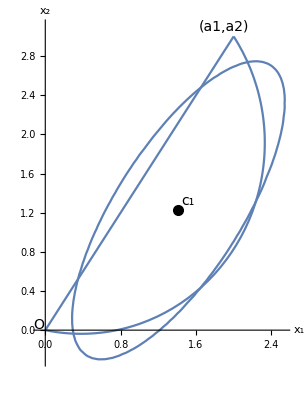

```mathematica
(*Пример расчета*)
a1 = 2;
a2 = 3;
T = Pi;
a3 = Pi;
XC = FindMoments[a1,a2,a3,T][[1]];
YC = FindMoments[a1,a2,a3,T][[2]];
A = a1/a2*YC;
T2=FindT[a1,a2,a3,T];
x11 = FindX12[a1,a2,a3,T][[1]];
B = x11/.t->T2;
Show[ParametricPlot[{FindX12[a1,a2,a3,T][[1]],FindX12[a1,a2,a3,T][[2]]},{t,0,T}, AxesStyle->Arrowheads[{0.0, 0.05}], AxesLabel->{Subscript[x,1],Subscript[x,2]}, LabelStyle->FontSize->14], Plot[a2/a1 s, {s,0, a1}],
Graphics[{PointSize[0.02],Point[{{XC,YC}},VertexColors->{Black}]}],
Graphics[Text[Style["(a1,a2)",FontSize->14],{a1-0.1,a2+0.1}]],
Graphics[Text[Style[Subscript[c,1], FontSize->14],{XC+0.1,YC+0.1}]],
ShowEllipse2[a1,a2,a3,T],
Graphics[Text[Style["O",FontSize->14],{0-0.07,0+0.05}]],
PlotRange->All]
```

```mathematica
(*Исследование момента инерции круговой оси (W,J)*)
ClearAll[J1,J2,K12]
J= J1 Cos[teta]^2-2K12 Sin[teta]Cos[teta]+J2 Sin[teta]^2;
Solve[Simplify[D[J, teta]]==0,teta]
```

```mathematica
k1 =Simplify[1/2 ArcTan[(-(2 K12)/(√(J1^2-2 J1 J2+J2^2+4 K12^2)))/(J1/(√(J1^2-2 J1 J2+J2^2+4 K12^2))-J2/(√(J1^2-2 J1 J2+J2^2+4 K12^2)))]];
k2 =Simplify[1/2 ArcTan[((2 K12)/(√(J1^2-2 J1 J2+J2^2+4 K12^2)))/(-J1/(√(J1^2-2 J1 J2+J2^2+4 K12^2))+J2/(√(J1^2-2 J1 J2+J2^2+4 K12^2)))]];
```

-1/2 ArcTan[(2 K12)/(J1-J2)]

-1/2 ArcTan[(2 K12)/(J1-J2)]

```mathematica
Simplify[J/.teta->k1]
```

```mathematica
(2 K12^2)/((J1-J2) √(1+(4 K12^2)/(J1-J2)^2))+J1 Cos[1/2 ArcTan[(2 K12)/(J1-J2)]]^2+J2 Sin[1/2 ArcTan[(2 K12)/(J1-J2)]]^2
```

(2 K12^2)/((J1-J2) √(1+(4 K12^2)/(J1-J2)^2))+J1 Cos[1/2 ArcTan[(2 K12)/(J1-J2)]]^2+J2 Sin[1/2 ArcTan[(2 K12)/(J1-J2)]]^2

```mathematica
J= J1 Cos[teta]^2-2K12 Sin[teta]Cos[teta]+J2 Sin[teta]^2;

Simplify[TrigExpand[J/.teta->k1]]
```

1/2 (J1+J2+J1 √((J1^2-2 J1 J2+J2^2+4 K12^2)/(J1-J2)^2)-J2 √((J1^2-2 J1 J2+J2^2+4 K12^2)/(J1-J2)^2))

```mathematica
ClearAll[J1,J2,K12, Jmaxmin1, Jmaxmin2, J];
J= J1 Cos[teta]^2-2K12 Sin[teta]Cos[teta]+J2 Sin[teta]^2;
a3 = Pi/4;
T =Pi/4;
Jmaxmin1[J1_,K12_,J2_]=Simplify[TrigExpand[J/.teta->k1]]
```

1/2 (J1+J2+J1 √((J1^2-2 J1 J2+J2^2+4 K12^2)/(J1-J2)^2)-J2 √((J1^2-2 J1 J2+J2^2+4 K12^2)/(J1-J2)^2))

```mathematica
Jmaxmin[J1_,K12_,J2_]= (J1+J2)/2 + Sqrt[((J1-J2)/2)^2 + K12^2]
```

(J1+J2)/2+√(1/4 (J1-J2)^2+K12^2)

```mathematica
JmaxPlot[a1_,a2_,a3_,T_]:=Module[{J1,K12, J2,result},
result = FindMoments[a1,a2,a3,T];
J1 =result[[3]];
J2 = result[[5]];
K12 =  result[[4]];
Jmaxmin[J1,K12,J2]]

Plot3D[{JmaxPlot[a1,a2,a3,T]}, {a1, 0, 2},{a2,0,2}]
```

```mathematica
data=Table[JmaxPlot[a1,a2,a3,T],{a1, 10, 20},{a2,0,9}];
```

```mathematica
ListPlot3D[data,Mesh->None,InterpolationOrder->3,ColorFunction->"SouthwestColors"]
```

-Graphics3D-

```mathematica
a1 =a2=a3=3
f[t_] = -(t-Sin[t]) /((Sin[t/2])^2)+8 a3/a2^2;
```

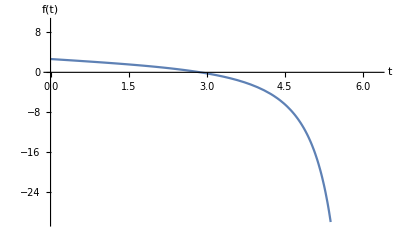

```mathematica
Plot[f[t],{t,0,2Pi}, AxesStyle->Arrowheads[{0.0, 0.05}], AxesLabel->{t,"f(t)"}, LabelStyle->FontSize->14, PlotRange->{-30,10}]
```

```mathematica
ClearAll[tz, a2,p1,p2];
p1=0.5p3 a2 Cot[tz/2];
p2=-0.5p3 a2 ;
R = (p1/p3)^2 + (p2/p3)^2
```

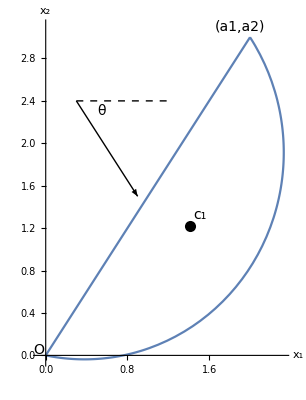

```mathematica
a1 = 2;
a2 = 3;
T = Pi;
a3 = Pi;
XC = FindMoments[a1,a2,a3,T][[1]];
YC = FindMoments[a1,a2,a3,T][[2]];
A = a1/a2*YC;
T2=FindT[a1,a2,a3,T];
x11 = FindX12[a1,a2,a3,T][[1]];
B = x11/.t->T2;
Show[ParametricPlot[{FindX12[a1,a2,a3,T][[1]],FindX12[a1,a2,a3,T][[2]]},{t,0,T}, AxesStyle->Arrowheads[{0.0, 0.05}], AxesLabel->{Subscript[x,1],Subscript[x,2]}, LabelStyle->FontSize->14], Plot[a2/a1 s, {s,0, a1}],
Graphics[{PointSize[0.02],Point[{{XC,YC}},VertexColors->{Black}]}],
Graphics[Arrow[{{0.3,2.4},{0.9,1.5}}]],
Graphics[{Dashed,Line[{{0.3,2.4},{1.2,2.4}}]}],
Graphics[Text[Style[θ,FontSize->14],{0.55,2.3}]],
Graphics[Text[Style["(a1,a2)",FontSize->14],{a1-0.1,a2+0.1}]],
Graphics[Text[Style[Subscript[c,1], FontSize->14],{XC+0.1,YC+0.1}]],
Graphics[Text[Style["O",FontSize->14],{0-0.07,0+0.05}]],
PlotRange->All]
```